## Single lepton spectrum

```mathematica
SetDirectory["~/mathematica/multileptons"]; 
Needs["PlotLegends`"]
```

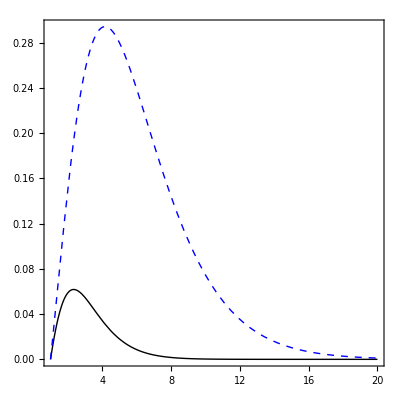

```mathematica
Block[{plot},
 plot = ShowLegend[
   Plot[
    Evaluate[
     4 1/(2 π^2) Table[(X^2 - 1)/(
       Exp[2 π/(11.24 y) X] + 1), {y, {.5, 1}}]], {X, 1, 20},
    PlotStyle -> {{Black}, {Blue, Dashed}},
    Frame -> True,
    FrameLabel -> {"x"},
    FrameTicks -> {{All, None}, {All, None}},
    AxesOrigin -> {0, 0},
    PlotRange -> All,
    AspectRatio -> 1
    ], {{{Graphics[{Blue, Dashed, Line[{{0, 0}, {1.5, 0}}]}], 
      "y = 1"}, {Graphics[{Black, Line[{{0, 0}, {1.5, 0}}]}], "y = .5"}}, 
    LegendPosition -> {1.1, -.4}}
   ];
 Export["single-lepton-spectrum-times4.eps", plot, "eps"];
 plot
 
 ]
```

```mathematica
1.14 0.3
```

0.342

```mathematica
19.8 0.064
```

1.2672

```mathematica
0.016 4
```

0.064